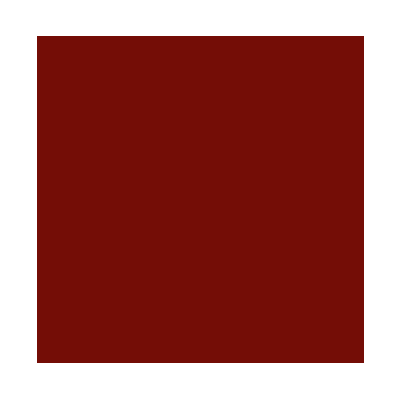

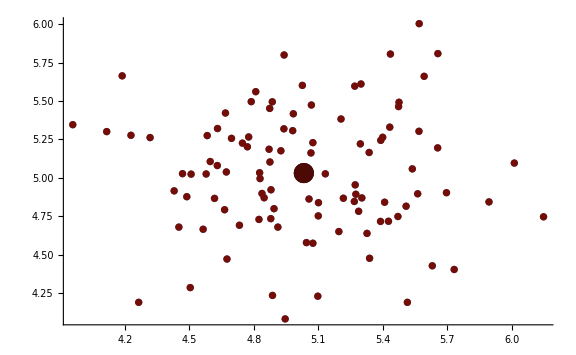

```mathematica
directory = "D:/Programming/AI/KMeans/Release/";
Run[directory<>"Kmeans.exe"];
chosenFile=ReadList[directory<>"datachoice.txt",String];
chosenFile=chosenFile[[1]];

dimensions=2;
data = ReadList[chosenFile,Table[Number,dimensions]];
colorData = ColorData[16];

K=ReadList[directory<>"K.txt",Number];
K=K[[1]];
clusters=ReadList[directory<>"clusters.txt",Table[Number,K]];
centers = ReadList[directory<>"centers.txt",Table[Number,dimensions]];

colorDataArr=Table[colorData[k],{k,1,K}];
ArrayPlot[{Table[k,{k,1,K}]},ColorRules->Table[k->colorDataArr[[k]],{k,1,K}]]
colorPoints = If[Length[centers]>1,Table[Blend[colorDataArr,clusters[[k]]],{k,1,Length[clusters]}],Table[colorDataArr[[1]],{k,1,Length[clusters]}]];

clustersPlot=ListPlot[Table[Style[data[[k]],colorPoints[[k]]],{k,1,Length[clusters]}],ImageSize->Large,PlotRange->All];
(*centersPlot=ListPlot[centers,PlotStyle->{Black, PointSize[0.03]},PlotRange->All];*)
centersPlot=ListPlot[Table[Style[centers[[k]],Darker[colorDataArr[[k]]]],{k,1,K}],PlotStyle->PointSize[0.025],PlotRange->All];
finalPlot=Show[clustersPlot,centersPlot]
rngStr="pic"<>ToString[RandomInteger[{10000,99999}]]<>".jpeg";
Export[directory<>rngStr,finalPlot,"JPEG"];
```